# Practical 7 :: Plotting the Characteristic for the First Order PDE

## A general quasi-linear PDE is : a (x,y,u) u_x + b(x,y,u) u_y - c(x,y,u) = 0 The characteristic equations of the quasi-linear equation : dx/dt = a (x,y,u) dy/dt = b (x,y,u) du/dt = c (x,y,u) Equivalently characteristic equations of the above equation in the non - parametric form are : dx/a = dy/b = du/c Integrate the above and plot the solutions

Ques 1.    y u_x  +  x u_y = 0
The characteristic system is given by dx/y = dy/x = du=0 and the characteristic equations are given by x^2 + y^2=c_1  and u=c_2.  Taking c_1= 1 and  u = c_2 . Taking c_1 =1 and 3 and c_2= 3 and 8.

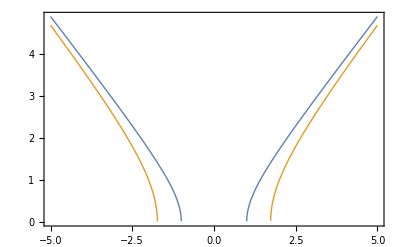

```mathematica
Plot[{Sqrt[x^2-1], Sqrt[x^2-3]}, {x,-5,5}, PlotStyle->Thick, Frame->True]
```

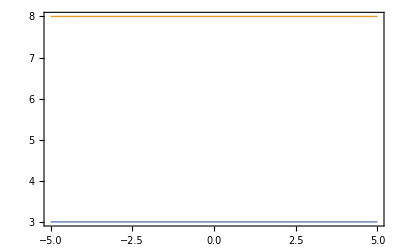

```mathematica
Plot[{3,8}, {x, -5, 5}, PlotStyle->Thick, Frame->True]
```

Ques 2.    x u_x  +  y u_y = u
The characteristic system is given by dx/x = dy/y = du/u and the characteristic equations are given by y/x = c_1 and u/x = c_2. Taking c_1= 1 and 3 and c_2= 3 and 8.

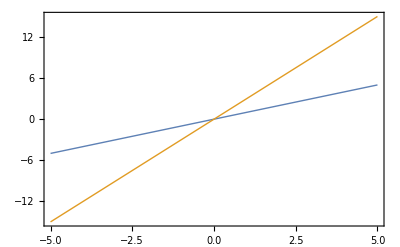

```mathematica
Plot[{x, 3x}, {x, -5, 5}, PlotStyle->Thick, Frame->True]
```

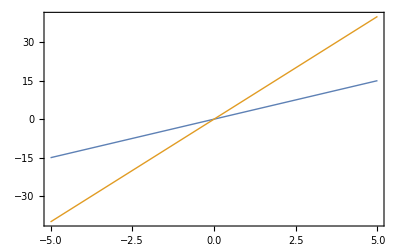

```mathematica
Plot[{3x,8x}, {x, -5, 5}, PlotStyle->Thick, Frame->True]
```

Ques 3.     (y+xu) u_x  - (x+uy) u_y = x^2 - y^2
The characteristic system is given by dx/y+ux = dy/-(x+uy) = du/x^2-y^2 and the characteristic equations are given by xy+u = c_1 and x^2+y^2-u^2 = c_2. Taking c_1= 0 and 9 and c_2= 0 and 10.

```mathematica
Plot3D[{-x*y, -x*y+9}, {x, -5, 5}, {y,-5,5},PlotStyle->Thick]
```

-Graphics3D-

```mathematica
Plot3D[{Sqrt[x^2 +y^2], Sqrt[x^2+ y^2 - 10]}, {x,-5,5},{y, -10, 10},PlotStyle->Thick]
```

-Graphics3D-

Ques 4.    x u_x  +  y u_y = u
The characteristic system is given by dx/x = dy/y = du/u and the characteristic equations are given by y/x = c_1 and u/x = c_2. Taking c_1= 1 and 3 and c_2= 3 and 8.